# Program for the computation of the functional determinant of the Laplacian operator

Gonzalo Sancho Garrido

We first define the function testM, which tells us whether our parameters ,  and  correspond to a matrix  which belongs in .

```mathematica
testM[α_,β_,n1_]:=If[-1<=n1<=1,If[0<=α<=Pi,If[-Pi/2<=β<=Pi/2,If[0<=α+β<=Pi,If[0<=α-β<=Pi,1,0],0],0],0],0]
```

Now, we create a function that calculates the determinant of  , which will be useful to find out whether our matrix  belongs in  or not.

```mathematica
detDU[α_,β_,n1_,L_]:=L(Cos[α] -Cos[β])-2(Sin[α]+n1 Sin[β])
```

Similarly to testM, we can define a function that returns 1 if  belongs to the Von Neumann-Krein extension, and 0 if it doesn’t.

```mathematica
testVNK[α_,β_,n1_,L_]:=If[n1==1,If[-Pi/2<=α<=0,If[0<=β<=Pi/2,If[α==-β,If[β == ArcTan[2/L],1,0],0],0],0],0]
```

The formula for  will be different depending of the values of  and , so we need to define a function that computes it for each of the different cases.

```mathematica
dzeta1[α_,β_,n1_,L_]:=FullSimplify[-Log[Abs[(2L(Cos[α]-Cos[β])-4(Sin[α]+n1 Sin[β]))/(Cos[α]+Cos[β])]],L>0]
```

```mathematica
dzeta2[α_,β_,n1_,L_]:=FullSimplify[-Log[Abs[(L(Cos[α]-Cos[β])-2(Sin[α]+n1 Sin[β]))/Sin[α]]],L>0]
```

```mathematica
dzeta3[α_,β_,n1_,L_]:=FullSimplify[-Log[2L],L>0]
```

```mathematica
dzeta4[α_,β_,n1_,L_]:=FullSimplify[-Log[Abs[(L(2Cos[α+L Sin[α]]))/Cos[α]]],L>0]
```

```mathematica
dzeta5[α_,β_,n1_,L_]:=FullSimplify[-2Log[L],L>0]
```

```mathematica
dzeta6[α_,β_,n1_,L_]:=FullSimplify[-Log[L^3/6],L>0]
```

We can now define the general function dzeta, giving us the value of the derivative of the zeta function in all cases.

```mathematica
dzeta[α_,β_,n1_,L_]:=Which[testM[α,β,n1]==1,If[Refine[detDU[α,β,n1,L]==0,L>0],If[α==Pi/2,dzeta5[α,β,n1,L],dzeta4[α,β,n1,L]],If[Abs[β]==Pi-α,If[α==Pi,dzeta3[α,β,n1,L],dzeta2[α,β,n1,L]],dzeta1[α,β,n1,L]]],testVNK[α,β,n1,L]==1,dzeta6[α,β,n1,L],True,"The values of the parameters are not valid."]
```

Since the determinant of the Laplacian and the derivative of the zeta function are related via , we can use the function above to create a similar one for the determinant of the Laplacian.

```mathematica
DetLap[α_,β_,n1_,L_]:=Which[testM[α,β,n1]==1,Exp[-dzeta[α,β,n1,L]],testVNK[α,β,n1,L]==1,Exp[-dzeta[α,β,n1,L]],True,"The values of the parameters are not valid."]
```

```mathematica
dzeta[0,0,1,L]
```

-Log[2 L]

```mathematica
dzeta[Pi,0,1,L]
```

-Log[2 L]

```mathematica
dzeta[Pi/2,-Pi/2,1,L]
```

-2 Log[L]

```mathematica
dzeta[3Pi/4,0,1,L]
```

Log[(2-√2)/(4 √2+2 (2+√2) L)]

```mathematica
DetLap[Pi,0,1,L]
```

2 L

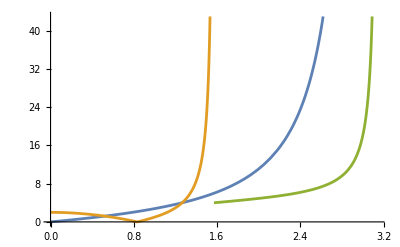

```mathematica
Plot[{DetLap[α,0,1,1],DetLap[α,-α,1,1],DetLap[α,Pi-α,1,1]},{α,0,Pi}]
```

```mathematica
DetLap[0.99Pi,0,1,L]
```

254.627+8104.36 L

```mathematica
DetLap[Pi/2,-Pi/2,1,L]
```

L^2